```mathematica
Solve[{2α-3γ== 1, α+γ == 0, -2α+β== 0},{α,β,γ}]
```

{{α→1/5,β→2/5,γ→-1/5}}

```mathematica
rlist={{0.006,1.9*100/2}, {0.025,2.6*100/2.1},{0.016,2.5*100/2.2},{0.09,3.5*100/2},{0.034,1*100/0.7},{0.127,1.25*100/0.7}}
```

{{0.006,95.},{0.025,123.81},{0.016,113.636},{0.09,175.},{0.034,142.857},{0.127,178.571}}

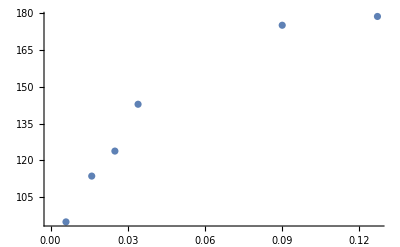

```mathematica
ListPlot[rlist]
```

```mathematica
rlistb = Table[{rlist[[i,1]]^(1/2),rlist[[i,2]]^5},{i,1,Length[rlist]}]
```

{{0.0774597,7.73781×10^9},{0.158114,2.90918×10^10},{0.126491,1.8949×10^10},{0.3,1.64131×10^11},{0.184391,5.9499×10^10},{0.356371,1.81577×10^11}}

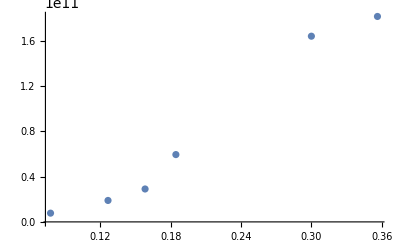

```mathematica
ListPlot[rlistb]
```

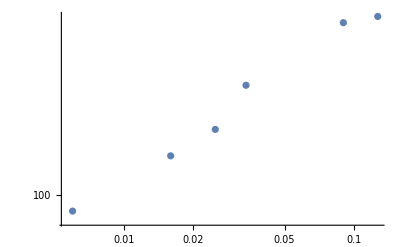

```mathematica
ListLogLogPlot[rlist]
```

```mathematica
1.5*10^11/(10^9)
```

150.

```mathematica
rlistbo = Table[{rlistb[[i,1]],rlistb[[i,2]]/10^9},{i,1,Length[rlist]}]
```

{{0.0774597,7.73781},{0.158114,29.0918},{0.126491,18.949},{0.3,164.131},{0.184391,59.499},{0.356371,181.577}}

```mathematica
LinearModelFit[rlistbo,x,x]
```

FittedModel[-64.532+705.153 x]

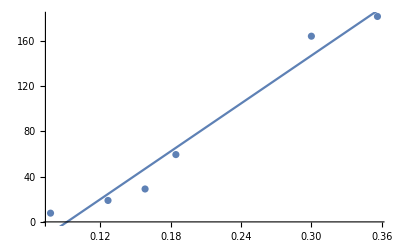

```mathematica
Show[ListPlot[rlistbo],Plot[-64.53195648857728+705.1532929641097 x,{x,0,0.4}]]
```

```mathematica
rlist
```

{{0.006,95.},{0.025,123.81},{0.016,113.636},{0.09,175.},{0.034,142.857},{0.127,178.571}}

```mathematica
Log[rlist]
```

{{-5.116,4.55388},{-3.68888,4.81874},{-4.13517,4.733},{-2.40795,5.16479},{-3.38139,4.96185},{-2.06357,5.18499}}

```mathematica
LinearModelFit[Log[rlist],x,x]
```

FittedModel[5.66368+0.219536 x]

```mathematica
2/5.
```

0.4

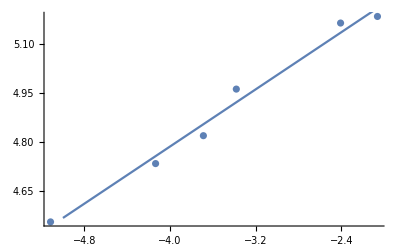

```mathematica
Show[ListPlot[Log[rlist]],Plot[5.663675090017619+0.2195362340144489 x,{x,-5,-2}]]
```

```mathematica
Log[rlist]
```

```mathematica
0.7/3
```

0.233333

```mathematica
Simplify[Log[c]+2/5 Log[t]]
```

Log[c]+(2 Log[t])/5

```mathematica
Log[2.]+2/5 Log[3]
```

1.13259

```mathematica
Log[2.*3^(2/5)]
```

1.13259

```mathematica
Exp[5*5.66]*1.2
```

2.34269×10^12